## Elementos da Wolfram Language (do Mathematica)

### Para executar uma célula de input (shift + Enter)

```mathematica
1+2
```

3

## Escrevendo funções: nomeFunção[argumentos]:= corpoFunção

### Soma de dois números

```mathematica
Soma[a_Integer,b_Integer]:=a+b;
```

```mathematica
Soma[2,3]
```

```mathematica
Soma[2.0,3]
```

```mathematica
Soma[a_,b_]:=a+b;
```

```mathematica
Soma[2.0,3]
```

```mathematica
Soma[{2,3,4},{5,6,7}]
```

### Fatorial (treinando recursão...)

```mathematica
Fat[0]:=1;
```

```mathematica
Fat[0]
```

```mathematica
Fat[5]
```

Fat[5]

```mathematica
Fat[n_Integer/;n>0]:=n*Fat[n-1];
```

```mathematica
Fat[-5]
```

Fat[-5]

```mathematica
Fat[8]
```

### Função pura (Exemplo: Dado um número, calcular seu quadrado mais 7)

```mathematica
(#^2+7)&[2]
```

11

```mathematica
(#^2+7)&@2
```

```mathematica
(#^2+7)&/@Range[1,10]
```

## Algumas funções nativas

### Table

```mathematica
Table[a,5]
```

{a,a,a,a,a}

#### Números de 1 a 10

```mathematica
Table[x,{x,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

#### Quadrado dos números de 1 a 10

```mathematica
Table[x^2,{x,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

#### Fatorial dos números de 1 a 10

```mathematica
Table[Fat[x],{x,1,10}]
```

#### Pares ordenados com os números de 1 a 10 e seus quadrados

```mathematica
Table[{x,x^2},{x,1,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

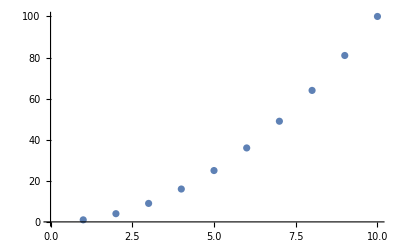

```mathematica
ListPlot[%]
```

#### Matriz 3 x 4 cujas células são a soma da linha com a coluna

```mathematica
Table[x+y,{x,1,3},{y,1,4}]
```

```mathematica
Table[x+y,{x,1,3},{y,1,4}]//MatrixForm
```

### Range, e RandomInteger

```mathematica
Range[0,9]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
RandomInteger[{0,1},10]
```

{1,1,1,1,1,0,0,1,0,1}

```mathematica
Table[RandomInteger[{0,1},10],5]
```

{{1,1,1,0,1,0,0,1,1,1},{1,0,0,0,0,1,0,0,0,0},{0,1,0,1,0,0,0,0,1,1},{0,0,1,1,0,0,1,0,1,1},{1,0,0,1,1,0,0,0,0,1}}

### Definição de função, e função pura

```mathematica
SomaUm[x_]:=x+1;
```

```mathematica
SomaUm[9]
```

10

```mathematica
(#+1)&[9]
```

10

### Map (e sua notação infixada)

```mathematica
Map[Sqrt,{1,4,9,16}]
```

```mathematica
Sqrt[#]&/@{1,4,9,16}
```

```mathematica
Map[Total[#]&,{1,2,3,4}]
```

Total::normal: Nonatomic expression expected at position 1 in Total[1].

Total::normal: Nonatomic expression expected at position 1 in Total[2].

Total::normal: Nonatomic expression expected at position 1 in Total[3].

General::stop: Further output of Total::normal will be suppressed during this calculation.

{Total[1],Total[2],Total[3],Total[4]}

```mathematica
Map[Total[#]&,{{1,2,3,4}}]
```

```mathematica
Map[Total[#]&,{{1,2,3,4},{5,6,7,8},{9,10,11,12}}]
```

```mathematica
Total[{{1,2,3,4},{5,6,7,8},{9,10,11,12}}]
```

```mathematica
Map[SomaUm[#]&,Range[0,9]]
Map[SomaUm,Range[0,9]]
```

{1,2,3,4,5,6,7,8,9,10}

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Map[(#+1)&,Range[0,9]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
{Range[0,9],Range[0,4]}
```

{{0,1,2,3,4,5,6,7,8,9},{0,1,2,3,4}}

```mathematica
Map[Length,{Range[0,9],Range[0,4]}]
Map[Length[#]&,{Range[0,9],Range[0,4]}]
```

{10,5}

{10,5}

```mathematica
Length/@{Range[0,9],Range[0,4]}
Length[#]&/@{Range[0,9],Range[0,4]}
```

{10,5}

{10,5}

```mathematica
Map[(#+1)&,Range[0,9]]
```

```mathematica
(#+1)&/@Range[0,9]
```

{1,2,3,4,5,6,7,8,9,10}

### Execução do AC da FCI (binário, bidimensional)

```mathematica
ListAnimate[ArrayPlot[#]&/@CellularAutomaton[
      { (#/.testRule)&,
        {},
        {1,1}
        },fciIC,32],AnimationRate->1]
```

```mathematica
CellularAutomaton[
      { (#/.testRule)&,
        {},
        {1,1}
        },fciIC,32]
```

```mathematica
{{a_,b_,c_},{d_,e_,f_},{g_,h_,i_}}//MatrixForm
```

(a_ | b_ | c_
d_ | e_ | f_
g_ | h_ | i_)

```mathematica
testRule={{a_,b_,c_},{d_,e_,f_},{g_,h_,i_}}->Replace;
```

```mathematica
ArrayPlot[#]&/@
CellularAutomaton[
      { (#/.testRule)&,
        {},
        {1,1}
        },fciIC,32]
```

### Caracteres especiais, por meio de esc-esc

```mathematica
α
```

```mathematica
∧
```

```mathematica
≠
```

```mathematica
x⟦2⟧
```

```mathematica
Range[0,9]⟦3⟧
```

2

```mathematica
Part[Range[0,9],3]
```

2

```mathematica
Range[0,9]⟦3⟧
```

2

```mathematica
α
```

```mathematica
2^4
```

16

### GatherBy, Select e Cases

```mathematica
GatherBy[Range[0,20],EvenQ]
GatherBy[Range[0,20],EvenQ[#]&]
```

{{0,2,4,6,8,10,12,14,16,18,20},{1,3,5,7,9,11,13,15,17,19}}

{{0,2,4,6,8,10,12,14,16,18,20},{1,3,5,7,9,11,13,15,17,19}}

```mathematica
Select[Range[0,20],EvenQ]
Select[Range[0,20],EvenQ[#]&]
```

{0,2,4,6,8,10,12,14,16,18,20}

{0,2,4,6,8,10,12,14,16,18,20}

```mathematica
Cases[Range[0,20],x_/;EvenQ[x]]
```

{0,2,4,6,8,10,12,14,16,18,20}

### Position

#### Dada uma lista de objetos quaisquer, encontrar as posições onde se encontram números inteiros maiores que 5

```mathematica
listaobjetos={17,Graph[{1->2,2->3,3->1,3->4,4->1}],7,5.0,5,6,{6,7,9},"Olá!",1,-3,{1,2,3}};
```

```mathematica
Position[listaobjetos,x_Integer/;x>5]
```

### Join e Union

```mathematica
Join[{3,2},{2,1,2},{}]
```

{3,2,2,1,2}

```mathematica
Union[{3,2},{2,1}]
```

{1,2,3}

### MapThread

```mathematica
MapThread[Times,{{1,2,3,4,5},{5,6,7,8,9}}]
MapThread[Times[#1,#2]&,{{1,2,3,4,5},{5,6,7,8,9}}]
```

{5,12,21,32,45}

{5,12,21,32,45}

```mathematica
MapThread[List,{{1,2,3,4,5},{5,4,3,2,1},{1,1,1,1,1}}]
```

{{1,5,1},{2,4,1},{3,3,1},{4,2,1},{5,1,1}}

### Head

```mathematica
Head[5]
```

Integer

```mathematica
Head[5.0]
```

```mathematica
Head[{1,2,3}]
```

List

```mathematica
Head[2+3+4]
```

```mathematica
Head[True]
```

```mathematica
Head["Boa noite!"]
```

```mathematica
Head[x]
```

Symbol

```mathematica
x=5;
Head[x]
```

```mathematica
ClearAll[x]
```

### Apply

```mathematica
Apply[Plus,{1,2,3,4}]
```

10

```mathematica
Plus@@{1,2,3,4}
```

```mathematica
Apply[Times,{1,2,3,4}]
```

```mathematica
Apply[f,{1,2,3,4}]
```

```mathematica
Apply[OddQ,{5}]
```

```mathematica
Apply[Sqrt,{1,4,9,16}]
```

```mathematica
Fat[0]:=1;
```

```mathematica
Fat[0]
```

```mathematica
Fat[5]
```

Fat[5]

```mathematica
Fat[n_Integer/;n>0]:=n*Fat[n-1];
```

```mathematica
Fat[-5]
```

```mathematica
Fat[8]
```

### CellularAutomaton

```mathematica
CellularAutomaton[{110,2,1},{0,1,0,0,0,0,0,0,0},10]
```

{{0,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,1},{1,1,0,0,0,0,1,1,1},{0,1,0,0,0,1,1,0,0},{1,1,0,0,1,1,1,0,0},{1,1,0,1,1,0,1,0,1},{0,1,1,1,1,1,1,1,1},{1,1,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,1,1}}

```mathematica
CellularAutomaton[{110,2,1},{0,1,0,0,0,0,0,0,0},10]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0
1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1
0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1)

```mathematica
CellularAutomaton[{110,2,1},{{1},0},10]
```

{{0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,1,1,0,1},{0,0,0,0,0,0,1,1,1,1,1},{0,0,0,0,0,1,1,0,0,0,1},{0,0,0,0,1,1,1,0,0,1,1},{0,0,0,1,1,0,1,0,1,1,1},{0,0,1,1,1,1,1,1,1,0,1},{0,1,1,0,0,0,0,0,1,1,1},{1,1,1,0,0,0,0,1,1,0,1}}

```mathematica
CellularAutomaton[{110,2,1},{{1},0},10]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1)

```mathematica
ArrayPlot[CellularAutomaton[{110,2,1},RandomInteger[{0,1},100],100]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{110,2,1},{{1},0},3300]]
```

### Visualização de conjunto de evoluções temporais

```mathematica
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,RandomInteger[{0,1},50],100],PlotLabel->#]&/@Range[0,255],16]]
```

```mathematica
ArrayPlot[CellularAutomaton[#,RandomInteger[{0,1},50],100]]&/@Range[0,16]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[RandomInteger[{0,1},50],6]//MatrixForm
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

### Regras de Substituição

#### Dada uma lista de números binários, trocar 0 por 1 e vice-versa

```mathematica
listabin=RandomInteger[1,20]
```

```mathematica
listabin/.{0->1,1->0}
```

#### Dada uma lista de números inteiros, trocar todos os pares por 0 e todos os ímpares por 1

```mathematica
listaint=RandomInteger[10,20]
```

```mathematica
listaint/.{(x_/;EvenQ[x])->0,(x_/;OddQ[x])->1}
```

### Exemplo de aplicação: Codificando uma mensagem

```mathematica
mensagemnormal="esta e uma mensagem normal";
```

```mathematica
regracodigo=MapThread[Rule,{alfabeto,alfabetoreverso}]
```

```mathematica
Characters[mensagemnormal]
```

```mathematica
Characters[mensagemnormal]/.regracodigo
```

```mathematica
StringJoin[%]
```